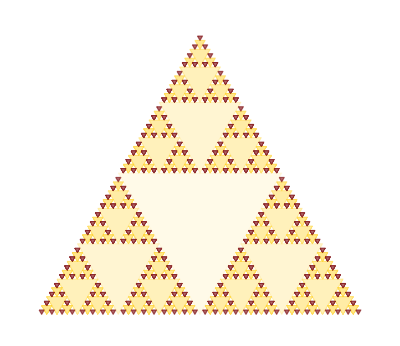

```mathematica
SetDirectory[NotebookDirectory[]];

layers=6; (*Number of nested layers of the pyramid*)
gradient="SolarColors"; (*Color scheme used*)

output={};
eqTriangle[length_,Δx_,Δy_,Δz_]:=Graphics[{Opacity[0],EdgeForm[Thick],Polygon[{{(-length/2)+Δx,Δy,Δz},{Δx,(length*Sqrt[3]/2)+Δy,Δz},{(length/2)+Δx,Δy,Δz}}]}];
radius[length_]:=length/Sqrt[3];
triangleUp[length_,Δx_,Δy_,numLayers_]:=Graphics[{Opacity[(layers-numLayers)/10],EdgeForm[Thickness[Small]],ColorData[gradient][numLayers],Polygon[{{(radius[length])*Cos[7π/6]+Δx,(radius[length])*Sin[7π/6]+Δy},{Δx,(radius[length])+Δy},{(radius[length])*Cos[11π/6]+Δx,(radius[length])*Sin[11π/6]+Δy}}]}];
triangleDown[length_,Δx_,Δy_,numLayers_]:=Graphics[{Opacity[(layers-numLayers)/10],EdgeForm[Thickness[Small]],ColorData[gradient][numLayers],Polygon[{{(radius[length])*Cos[7π/6]+Δx,-(radius[length])*Sin[7π/6]+Δy},{Δx,-(radius[length])+Δy},{(radius[length])*Cos[11π/6]+Δx,-(radius[length])*Sin[11π/6]+Δy}}]}];
sierpTriangle[length_,Δx_,Δy_,numLayers_]:=If[numLayers==layers,AppendTo[output,triangleUp[length,Δx,Δy,numLayers]];sierpTriangle[length/2,Δx,Δy,numLayers-1],AppendTo[output,triangleDown[length,Δx,Δy,numLayers]];If[numLayers==0,"Base reached",sierpTriangle[length/2,(radius[length])*Cos[7π/6]+Δx,(radius[length])*Sin[7π/6]+Δy,numLayers-1];sierpTriangle[length/2,Δx,(radius[length])+Δy,numLayers-1];sierpTriangle[length/2,(radius[length])*Cos[11π/6]+Δx,(radius[length])*Sin[11π/6]+Δy,numLayers-1]]];

sierpTriangle[16,0,0,layers];
Show[output]
Export["Sierpinski.Triangle.pdf",EvaluationNotebook[]];
```